### Parameter table

Parameter | Known | Unknown
Initial para. | P_0=0.0477 (2017) | □
mean para age | μ=0.32 (2017) | □
SD para age | σ=0.26 (2017) | □
donor age est | x=0.00643 (2014) | □
acute age est | y=0.00441 (2014) | □
maturation rate | □ | λ = 0.65-1 (?)
infectivity | □ | β naive = 18.13 (2015)
infectivity | □ | β acute = 3.2(2015)
clearance age | □ | x_c naive = 0.75(2015)
clearance age | □ | x_c acute = 0.021(2015)
clearance rate | □ | c naive = 4.25(2015)
clearance rate | □ | c acute=0.85(2015)
Reticulocyte pref | □ | Pr=150 (Cromer)
Donor pRBCs rem. | naive =2.7% init (2017) | □
Donor pRBCs rem. | acute = 32% init (2017) | □
Donor init. conc. | naive=3.1% (2017) | □
Donor init. conc. | acute = 3.6% (2017) | □
Donor init para. | naive=4.2% (2017) | □
Donor init para. | acute=4.5%(2017) | □
Final total para. | naive=0.66% | □
Final total para. | acute=0.33% | □

Above values all for WT recipient mice but
    - Data from 2015 come from identical procedure as 2017 except donor was rag1 -/-;

Treat 2015 infections as age-structure only for naive case

### Estimating susceptibility of acute versus naive RBCs (from Khoury 2015)

```mathematica
P=149;
x=0.00441;
y1=0.01;y2=0.02;y3=0.03;

SusTabTot=Table[(18 (1+(-1+P) x))/(1+(-1+P) i),{i,0.01,0.03,0.01}]
```

{11.9953,7.51218,5.46843}

(2) Preference applied to only reticulocytes

```mathematica
P=150;
x=0.00441;
y1=0.01;y2=0.02;y3=0.03;

SusTabRet=Table[(17+18 (-1+P) x)/((-1+P) i),{i,0.01,0.03,0.01}]
```

{19.3474,9.6737,6.44913}

### Parasite maturation model

```mathematica
ClearAll["Global`*"]
```

```mathematica
P0=0.0011;
μ=0.32;
σ=0.26;
c=3.92;
n=Ceiling[t*λ-x];
xr=1.;
A=2.6;
βu=9;
β0=0.4;
xc=0.9;
λ=0.6;
β[t_]=Piecewise[{{β0*A*x^(A-1)/xr^A, t≤1},{βu,t>1}}]; (*Time-dependent infectivity (parasite age dependent during first day) *)
```

```mathematica
Integrate[P2[0.5,x],{x,0,0.5}]
```

0.00750284

```mathematica
P2[1,0.1]
```

0.00924514

```mathematica
P2[t_,x_]=Piecewise[{
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ],x≥t*λ &&x<xc},
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ]*ⅇ^(-c/λ*(x-xc)),x≥t*λ &&x≥xc&& x-t*λ≤xc},
	{P0*PDF[NormalDistribution[μ,σ],x-t*λ]*ⅇ^(-c*t*λ),x≥t*λ && x≥ xc&& x-t*λ>xc},
	{βu^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-(n*c)/λ*(1-xc)),x<t*λ &&x<xc&& t*λ-x≥ 1-xc},
	{βu^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-c/λ*(t*λ-x-(n-1)*xc)),x<t*λ && x<xc&& t*λ-x< 1-xc},
	{βu^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-(n*c)/λ*(1-xc))*ⅇ^(-c/λ*(x-xc)),x<t*λ &&x≥xc&& t*λ-x≥ 1-xc},
	{βu^n*P0*PDF[NormalDistribution[μ,σ],n+x-t*λ]*ⅇ^(-c/λ*(t*λ-n*xc)),x<t*λ &&x≥xc&& t*λ-x<1-xc}
},0];
```

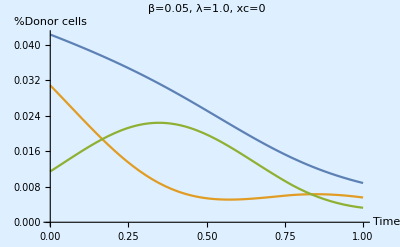

```mathematica
Plot[{Integrate[P2[t,x],{x,0,1.}],Integrate[P2[t,x],{x,0,0.5}],Integrate[P2[t,x],{x,0.5,1.}]},{t,0,1.}, PlotLabel-> "β=0.05, λ=1.0, xc=0",Background->LightBlue, AxesLabel-> {"Time","%Donor cells"}]
```

Naive host

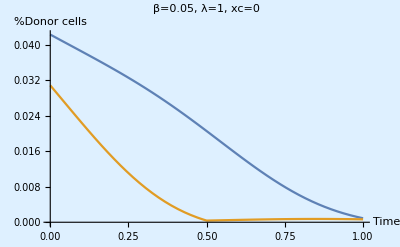

Acute host

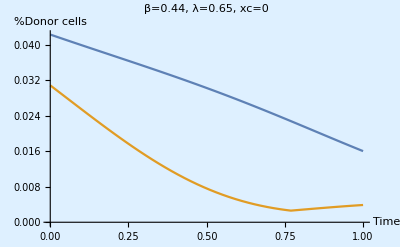

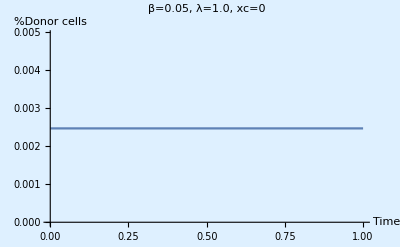

```mathematica
Plot[{Integrate[P2[t,x],{x,0,1.}]},{t,0,1.}, PlotLabel-> "β=0.05, λ=1.0, xc=0",Background->LightBlue, AxesLabel-> {"Time","%Donor cells"}]
```

From Khoury 2014 data, can explain 33% of the remaining donor pRBCs by age structure alone (assuming Pr=150)

```mathematica
9 cells per burst cell
Based on abundance -> 0.03*9 new donor pRBCs
Based on abundance and age structure
```

```mathematica
(0.036*(1+0.00643*149))/(0.964*(1+0.00441*149)+0.036*(1+0.00643*149))*9
```

0.380362

```mathematica
out=Integrate[P2[0,x],{x,0,1.}]
```

0.00659751